```mathematica
(*PES fitting; Quartic angle*)

(*Input data*)
SetDirectory["/Users/Sherina/Desktop/GAS/ANGLE/KS.KC.KN"];
```

```mathematica
PES=Import["PES_processed.txt","Table"];(*Unit: {rad, kJ/mol}*)

a0 = 178.72055265/180*Pi(*rad*);
```

```mathematica
Clear[k,a,d]
```

```mathematica
fit=FindFit[PES,k0+k2*(x-a0)^2+k4*(x-a0)^4,{ k0,k2,k4}, x](*kJ*mol^-1*rad^-2*)
```

{k0→-0.0155624,k2→84.2221,k4→23.8142}

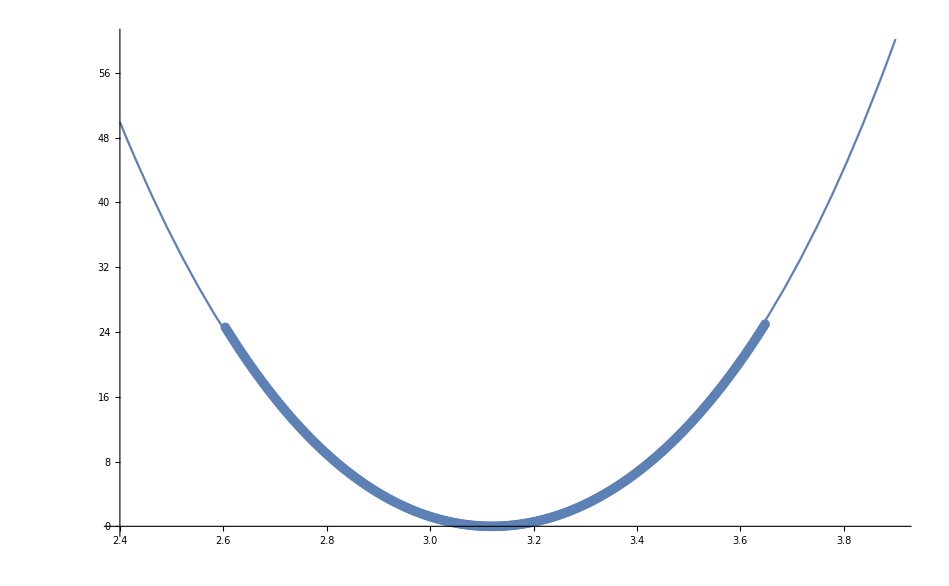

```mathematica
Show[Plot[fit[[1,2]]+fit[[2,2]]*(x-a0)^2+fit[[3,2]]*(x-a0)^4,{x,2.4,3.9},PlotRange->{{2.4,3.9},Automatic}],ListPlot[PES]]
```